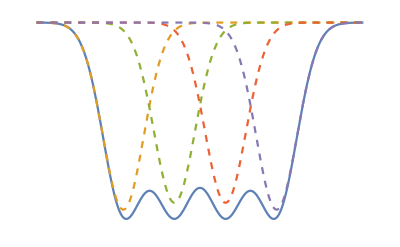

~/OneDrive - Rice University/Documents/Research/Optical tweezer on Fermi Hubbard/Notes/trap_superposition_4.pdf

```mathematica
f[x_]:=-Exp[-(2x^2)/w^2];
w=1;a=1.25;n=4;
lc=a Table[i,{i,(-(n-1))/2,(n-1)/2}];
Voff=Table[0.98,{i,n}];
Voff[[1]]=1.02;Voff[[-1]]=1.02;
Voff=Table[1,{i,n}];
(*lc={-1.49847148,-0.49383376,0.493833765,1.49847148} a;*)
Voff={1.0192159,0.98180606,0.98180606,1.0192159};
flist =Voff Table[f[x-lc[[i]]],{i,n}];
llist = Join[{Total@flist},flist];
Plot[llist,{x,-4w,4w},Axes->False,PlotStyle->Join[{Automatic},Table[Dashed,{i,n}]],PlotRange->{-1.1,0}]
Export["~/OneDrive - Rice University/Documents/Research/Optical tweezer on Fermi Hubbard/Notes/trap_superposition_"<>ToString[n]<>".pdf",%]
```